107.5

275

382.5

(13 π)/36

3804

1773.8

2314.62

{{R_x→-693.395-3219.43 Cos[θ_p],R_z→1487.02+3219.43 Sin[θ_p],R_(2 x)→-1080.41+904.806 Cos[θ_p],R_(2 z)→2316.98-904.806 Sin[θ_p]}}

{-693.395-3219.43 Cos[θ_p]}

{1487.02+3219.43 Sin[θ_p]}

{-1080.41+904.806 Cos[θ_p]}

{2316.98-904.806 Sin[θ_p]}

{√((-693.395-3219.43 Cos[θ_p])^2+(1487.02+3219.43 Sin[θ_p])^2)}

{√((-1080.41+904.806 Cos[θ_p])^2+(2316.98-904.806 Sin[θ_p])^2)}

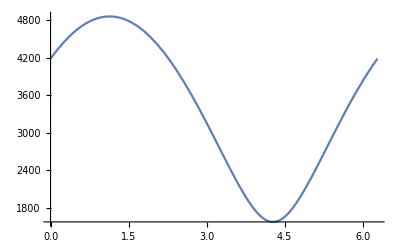

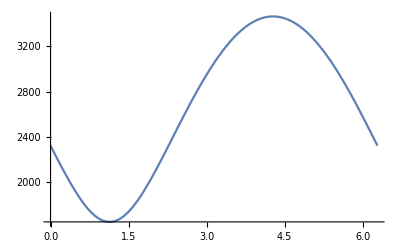

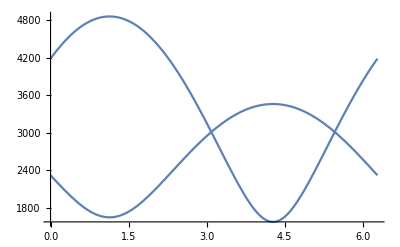

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ_p→-0.821137},{θ_p→3.09008}}

```mathematica
(*Primer eje, a b y c son las distancias a los rodamientos y a la rueda dentada*)
a1=107.5 (*dist al primer rodamiento*)
b1=275 (*dist a la rueda dentada*)
c1=382.5 (*dist al segundo rodamiento*)
Subscript[θ, b]=65π/180 (*angulo de la fuerza en el engranaje, esto puede ser cualquier cosa, solo hace falta dejarlo fijo, lo que va a cambiarme es el angulo en la polea, pero la fuerza que soporte el rodamiento será la misma*)
Wt=3804 (*fuerza en el engranaje*)
Wr=1773.8
Fp=2314.62 (*fuerza en la polea*)
sol=Solve[{Subscript[R, 1z]+Subscript[R, 2z]-Wt-Fp Sin[Subscript[θ, p]]==0, Subscript[R, 1x]+Subscript[R, 2x]+Wr+Fp Cos[Subscript[θ, p]]==0, -Subscript[R, 1x]a1-Wr b1-Subscript[R, 2x] c1==0, Subscript[R, 1z] a1-Wt b1+Subscript[R, 2z] c1==0}, {Subscript[R, 1x], Subscript[R, 1z], Subscript[R, 2x], Subscript[R, 2z]}]
R1x=sol[[All,1,2]]
R1z=sol[[All,2,2]]
R2x=sol[[All,3,2]]
R2z=sol[[All,4,2]]
Subscript[R, 1]=√(R1x^2+R1z^2)
Subscript[R, 2]=√(R2x^2+R2z^2)
p1=Plot[Subscript[R, 1], {Subscript[θ, p],0, 2π}]
p2=Plot[Subscript[R, 2], {Subscript[θ, p],0, 2π}]
Show[p1,p2] (*aca estoy mostrando las reacciones en función del ángulo de la polea*)
Solve[Subscript[R, 1]==Subscript[R, 2], Subscript[θ, p]](* cuando las reacciones son iguales estoy minimizando ambas fuerzas al mismo tiempo, esto me permite tener un eje mas chico en general*)
```

```mathematica
%77/.Subscript[θ, p]->-0.821137
```

```mathematica
{3015.12542083778}

Subscript[θ, p]=-0.8211366306636132
```

{3015.13}

```mathematica
-0.8211366306636132

Solve[{Subscript[R, 1z]+Subscript[R, 2z]-Wt-Fp Sin[Subscript[θ, p]]==0, Subscript[R, 1x]+Subscript[R, 2x]+Wr+Fp Cos[Subscript[θ, p]]==0, -Subscript[R, 1x]a1-Wr b1-Subscript[R, 2x] c1==0, Subscript[R, 1z] a1-Wt b1+Subscript[R, 2z] c1==0}, {Subscript[R, 1x], Subscript[R, 1z], Subscript[R, 2x], Subscript[R, 2z]}]
```

-0.821137

{{R_x→-2887.08,R_z→-869.347,R_(2 x)→-463.88,R_(2 z)→2979.23}}